```mathematica
Series[f[x],{x,a,3}]
```

f[a]+f'[a] (x-a)+1/2 f''[a] (x-a)^2+1/6 f^(3)[a] (x-a)^3+O[x-a]^4

```mathematica
Series[Cos[x],{x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+O[x]^11

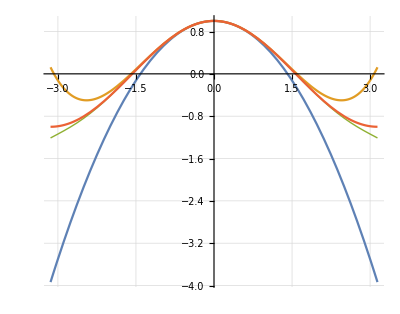

```mathematica
Plot[{1-x^2/2,1-x^2/2+(1/Factorial[4])x^4,1-x^2/2+(1/Factorial[4])x^4-(1/Factorial[6])x^6,Cos[x]},{x,-π,π},AspectRatio->Automatic,GridLines->Automatic,GridLinesStyle->{{Gray, Dotted}, {Gray, Dotted}},PlotStyle->{,,Thin}]
```

```mathematica
Series[E^x,{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

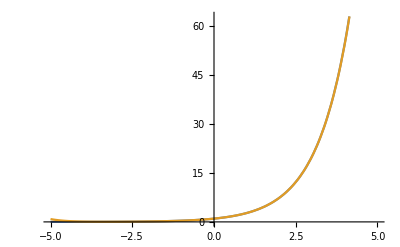

```mathematica
Plot[{E^x,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800},{x,-5,5}]
```

```mathematica
exp[x_]:=1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800
```

```mathematica
N[exp[3]]
```

20.0797

```mathematica
exP[x_]:=E^x
```

```mathematica
N[exP[3]]
```

20.0855

```mathematica
listaExp=N[Table[{x,exP[x]-exp[x]},{x,0,10,.5}]];
```

```mathematica
BarChart3D[listaExp,ChartStyle->"Pastel"]
```

-Graphics3D-

```mathematica
ExpToTrig[ⅇ^(ⅈ θ)]
```

Cos[θ]+ⅈ Sin[θ]

```mathematica
NestList[D[#,x]&,Sin[x],10]
```

{Sin[x],Cos[x],-Sin[x],-Cos[x],Sin[x],Cos[x],-Sin[x],-Cos[x],Sin[x],Cos[x],-Sin[x]}

```mathematica
%/.x->0
```

{0,1,0,-1,0,1,0,-1,0,1,0}

```mathematica
NestList[D[#,x]&,1/(1-x),10]
```

{1/(1-x),1/(1-x)^2,2/(1-x)^3,6/(1-x)^4,24/(1-x)^5,120/(1-x)^6,720/(1-x)^7,5040/(1-x)^8,40320/(1-x)^9,362880/(1-x)^10,3628800/(1-x)^11}

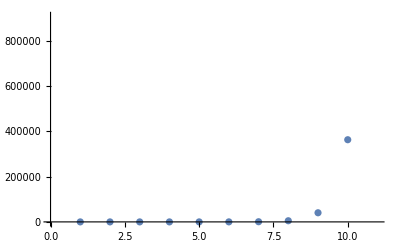

```mathematica
ListPlot[%/.x->0]
```

```mathematica
g[r_,θ_]:={r Cos[θ],r Sin[θ]}
```

```mathematica
arrow=
```